```mathematica
{tmax=N[22π],δ=0.05,c=0.1,q=1.}
```

{69.115,0.05,0.1,1.}

InterpolatingFunction[{{0., 69.115}}, <>]

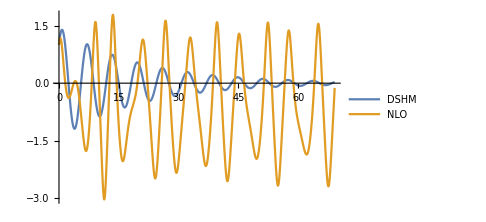

```mathematica
sol=NDSolveValue[{x''[t]+x[t]+0.05 x'[t]+0.5(x[t])^3+(x[t])^2==Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"]
Plot[{(*Cos[t]+Sin[t],*)1. ⅇ^(-0.05 t) (1. Cos[0.998749217771909 t]+1.0513149660756935 Sin[0.998749217771909 t]), sol[t]},{t,0,tmax},PlotLegends->{"DSHM","NLO"},ImageSize->Medium]
```

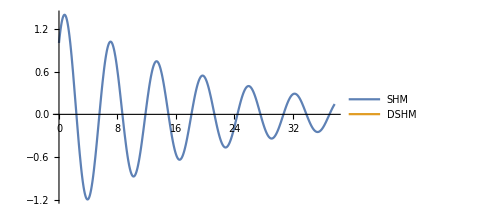
InterpolatingFunction[{{0., 37.6991}}, <>] -Graphics-

```mathematica
Module[{tmax=N[12π],δ=0.05,c=0.1,q=1.,x,t},sol=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==0,x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"]
Plot[{(*Cos[t]+Sin[t],*)1. ⅇ^(-0.05 t) (1. Cos[0.998749217771909 t]+1.0513149660756935 Sin[0.998749217771909 t]), sol[t]},{t,0,tmax},PlotLegends->{"SHM","DSHM","NLO"},ImageSize->Medium]]
```